# Cálculo de Linhas de Campo Magnetostático

## Antonio Carlos Siqueira de Lima Outubro de 2008

Using the Biot–Savart law, we obtain the well-known magnetic field B⃗(x⃗)∼{-y,x,0}/(x^2+y^2).

```mathematica
BInfiniteWire[{x_, y_}] =  {-y, x}/(x^2 + y^2);
```

Using the last result, we define the components of the magnetic field.

## Duas correntes de mesmo sentido

Instead of one infinite straight current, let us now deal with many of them. We choose 15 parallel currents at random positions and of random strengths. This system is translation-invariant along the wires. So, we restrict ourselves to the plane z=0.

```mathematica
xy2={{-1,0},{1,0}};
mp=Table[{Cos[60 Degree i],Sin[60 Degree i]},{i,0,5}]
```

{{1,0},{1/2,(√3)/2},{-1/2,(√3)/2},{-1,0},{-1/2,-(√3)/2},{1/2,-(√3)/2}}

```mathematica
(* SeedRandom[83569034823]
BField[{x_, y_}] = Plus @@ 
((Random[Real, {-1, 1}] BInfiniteWire[{x, y} - #])& /@ 
  (mps = Table[{Random[Real], Random[Real]}, {15}])) *)
```

```mathematica
BField2[{x_, y_}] = Plus @@ 
(( BInfiniteWire[{x, y} - #])& /@ 
  (xy2));
```

```mathematica
BField2posneg[{x_,y_}]={-y/((-1+x)^2+y^2)-(-1y)/((1+x)^2+y^2),(-1+x)/((-1+x)^2+y^2)+(-1(1+x))/((1+x)^2+y^2)} ;
```

```mathematica
BField6[{x_, y_}] = Plus @@ 
(( BInfiniteWire[{x, y} - #])& /@ 
  (mp));
```

```mathematica
BField6posneg[{x_,y_}]={-y/((-1+x)^2+y^2)-(-1y)/((1+x)^2+y^2)-(-(√3)/2+y)/((-1/2+x)^2+(-(√3)/2+y)^2)-(-1(-(√3)/2+y))/((1/2+x)^2+(-(√3)/2+y)^2)-((√3)/2+y)/((-1/2+x)^2+((√3)/2+y)^2)-(-1((√3)/2+y))/((1/2+x)^2+((√3)/2+y)^2),(-1+x)/((-1+x)^2+y^2)+(-1(1+x))/((1+x)^2+y^2)+(-1/2+x)/((-1/2+x)^2+(-(√3)/2+y)^2)+(-1(1/2+x))/((1/2+x)^2+(-(√3)/2+y)^2)+(-1/2+x)/((-1/2+x)^2+((√3)/2+y)^2)+(-1(1/2+x))/((1/2+x)^2+((√3)/2+y)^2)};
```

## Apelando para as funções já definidas no Mma

```mathematica
Needs["VectorFieldPlots`"]
```

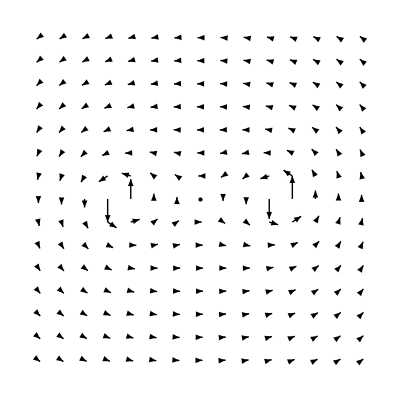

```mathematica
o1=VectorFieldPlot[BField2[{x,y}],{x,-2,2},{y,-2,2}]
```

```mathematica
Export["F:\\TE_I_2008-2\\h2condiguais.pdf", o1]
```

F:\TE_I_2008-2\h2condiguais.pdf

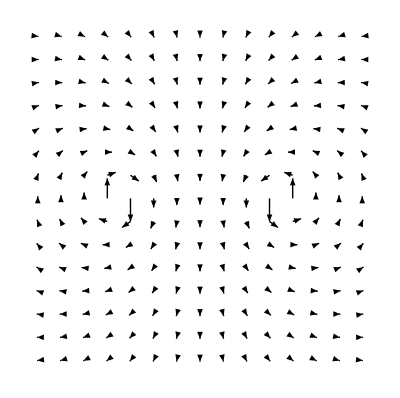

```mathematica
o2=VectorFieldPlot[BField2posneg[{x,y}],{x,-2,2},{y,-2,2}]
```

```mathematica
Export["F:\\TE_I_2008-2\\h2condicont.pdf", o2]
```

F:\TE_I_2008-2\h2condicont.pdf

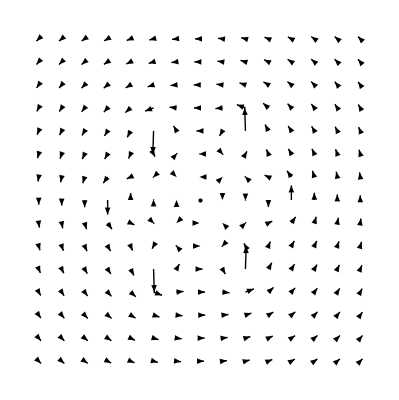

```mathematica
o3=VectorFieldPlot[BField6[{x,y}],{x,-2,2},{y,-2,2}]
```

```mathematica
Export["F:\\TE_I_2008-2\\h6condiguais.pdf", o3]
```

F:\TE_I_2008-2\h6condiguais.pdf

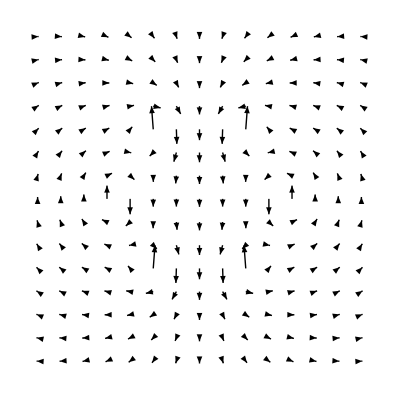

```mathematica
o4=VectorFieldPlot[BField6posneg[{x,y}],{x,-2,2},{y,-2,2}]
```

```mathematica
Export["F:\\TE_I_2008-2\\h6condcont.pdf", o4]
```

F:\TE_I_2008-2\h6condcont.pdf